Alternative Schreibweisen

Polarkoordinaten:{2 √5,ArcTan[1/2]}

Polarkoordinaten:{√2,-(3 π)/4}

Betrag z1: 2 √5

Betrag z2: √2

Winkel 1: 0.463648

Winkel 2: -2.35619

Winkel 1 Grad: 26.5651

Winkel 2 Grad: 360/π

Kartesisch bzw dezimale von z1: 4.+2. ⅈ

Kartesisch bzw dezimale von z2: -1.-1. ⅈ

Polarform: (2 √5) ⅇ^(ⅈ 0.463648)

Polarform: √2 ⅇ^(ⅈ (-2.35619))

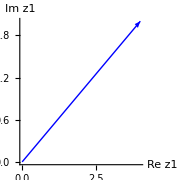

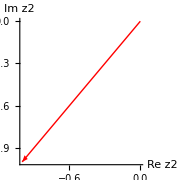

Ein paar Logarithmen, einfach ersetzen wie ihr braucht

ln(z1^2) -2ln(z1)= 0

ln(z2^2) -2ln(z2)= 2 ⅈ π

z1^2 -e^(2ln(z1))= 0

z2^2 -e^(2ln(z2))= 0

Komplexe Wurzeln z1:

{x→-(-2)^(1/5) (2+ⅈ)^(1/5)}
{x→(4+2 ⅈ)^(1/5)}
{x→(-1)^(2/5) (4+2 ⅈ)^(1/5)}
{x→-(-1)^(3/5) (4+2 ⅈ)^(1/5)}
{x→(-1)^(4/5) (4+2 ⅈ)^(1/5)}

Komplexe Wurzeln z2:

{x→(-1-ⅈ)^(1/5)}
{x→-(-1)^(1/5) (-1-ⅈ)^(1/5)}
{x→(-1)^(2/5) (-1-ⅈ)^(1/5)}
{x→-(-1)^(3/5) (-1-ⅈ)^(1/5)}
{x→(-1)^(4/5) (-1-ⅈ)^(1/5)}

```mathematica
z1 = 4+2I;
z2 = -1-I;
n=5; (*n-te Wurzel*)
Print["Alternative Schreibweisen"]
Print["Polarkoordinaten:",ToPolarCoordinates[ReIm[z1]]]
Print["Polarkoordinaten:",ToPolarCoordinates[ReIm[z2]]]
betrag = Abs[z1];
betrag2 = Abs[z2];
Print["Betrag z1: ",betrag]
Print["Betrag z2: ",betrag2]
winkel = N[Arg[z1]];
winkel2 = N[Arg[z2]];
Print["Winkel 1: ",winkel]
Print["Winkel 2: ",winkel2]
Print["Winkel 1 Grad: ", (180*winkel)/Pi]
Print["Winkel 2 Grad: ", (180*2)/Pi]
Print["Kartesisch bzw dezimale von z1: ", betrag*E^(I*winkel)]
Print["Kartesisch bzw dezimale von z2: ", betrag2*E^(I*winkel2)]
polar = With[{n=Abs[z1],a=N[Arg[z1  Degree]]},Defer[n E^(I a)]];
polar2 = With[{n=Abs[z2],a=N[Arg[z2 Degree]]},Defer[n E^(I a)]];
Print["Polarform: ",polar]
Print["Polarform: ",polar2]


Graphics[{Blue,ComplexVector[betrag, winkel]}, Axes->True, AxesLabel -> {"Re z1", "Im z1"}, ImageSize->Small]
Graphics[{Red,ComplexVector[betrag2, winkel2]}, Axes->True, AxesLabel -> {"Re z2", "Im z2"}, ImageSize->Small]
(*Einfach abändern wie ihr braucht*)
Print["Ein paar Logarithmen, einfach ersetzen wie ihr braucht"]
Print["ln(z1^2) -2ln(z1)= ", FullSimplify[Log[z1^2]-2*Log[z1]]]
Print["ln(z2^2) -2ln(z2)= ", FullSimplify[Log[z2^2]-2*Log[z2]]]
Print["z1^2 -e^(2ln(z1))= ", FullSimplify[z1^2-Exp[2*Log[z1]]]]
Print["z2^2 -e^(2ln(z2))= ", FullSimplify[z2^2-Exp[2*Log[z2]]]]
Print["Komplexe Wurzeln z1:"]
Column[Solve[x^n== z1, x]]

Print["Komplexe Wurzeln z2:"]
Column[Solve[x^n== z2, x]]



ComplexVector[r_,θ_]:=Arrow[{{0,0},{r*Cos[θ],r*Sin[θ]}}]
```